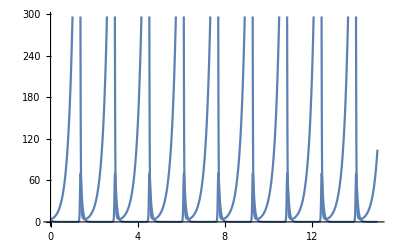

```mathematica
ode={
x'[t]==-16 x[t]+0.08 x[t] y[t],
y'[t]==4.5 y[t]-0.9 x[t] y[t]
};
init={x[0]==4,y[0]==4};
Tmax=24;
sol=NDSolve[Join[ode,init],{x[t],y[t]},{t,0,15}];
Plot[{x[t],y[t]}/.sol,{t,0,15}]
```

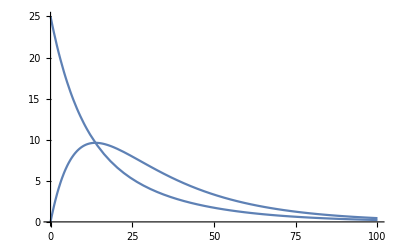

```mathematica
ode={
x'[t]==-(2/25) x[t]+(1/50) y[t],
y'[t]==(2/25) x[t]-(2/25) y[t]
};
init={x[0]==25,y[0]==0};
Tmax=60;
sol=NDSolve[Join[ode,init],{x[t],y[t]},{t,0,100}];
Plot[{x[t],y[t]}/.sol,{t,0,100}]
```